1/5 (-5+5 (Cos[x/5]+Sin[x/3])^3)

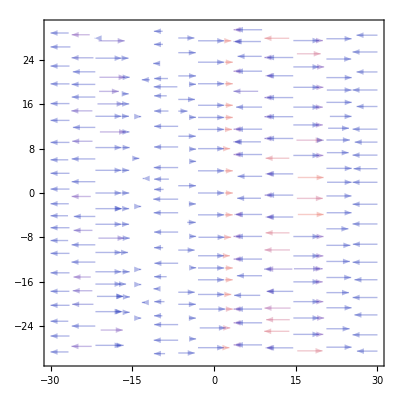
({3+(Cos[x/5]+Sin[x/3])^3,{3 (1/3 Cos[x/3]-1/5 Sin[x/5]) (Cos[x/5]+Sin[x/3])^2,0},1/150 (Cos[x/5]+Sin[x/3]) (34-27 Cos[(2 x)/5]+75 Cos[(2 x)/3]+26 Sin[(2 x)/15]-94 Sin[(8 x)/15]),0}
-Graphics-
-Graphics3D-)

```mathematica
ClearAll[Evaluate[Context[]<>"*"]];
z=x^2+y^5;
z=3+(Cos[x/5]+Sin[x/3])^3;
grad={gradu,gradv}=Grad[z,{x,y}];

(*通过grad 求原函数 *)
original=(∫_0^x graduⅆx/.{y->0})+∫_0^y gradvⅆy

(*梯度的散度也是拉普拉斯算子  div>0发散,<0汇聚, *)
div=Div[grad,{x,y}]//Simplify;
(*梯度场无旋 *)
curl=Curl[grad,{x,y}]//Simplify;
start=-30;end=-start;len=end;

{{z,grad,div,curl},
StreamPlot[grad,{x,start,end},{y,start,end},StreamStyle->{Opacity[0.3]}],
Plot3D[{z,div*5},{x,start,end},{y,start,end},PlotLegends->Automatic]

}//MatrixForm
```